```mathematica
ImportCsv[name_] := Import["~/workspace/PBLL/LieDetector/Analysis/" <> name <> ".csv","Dataset","HeaderLines"->1]
```

```mathematica
MeansFromCenter[name_, selectColumn_:"", selectValue_:""] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allDistances, allMeans},
columns = {"Combine Gaze X","Combine Gaze Y"};
dataset=If[StringLength[selectColumn]>0,Select[ImportCsv[name], #[selectColumn] == selectValue&], ImportCsv[name]];
allValues=Values[dataset[All,columns]];
center={Mean[allValues[All,1]],Mean[allValues[All,2]]};

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allDistances=((ArcLength[Line[{#,center}]])& /@ #)&/@groupedValues;
allMeans = (Mean[#])& /@ allDistances;
allMeans
]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

```mathematica
IndividualClassifierData[dataset_, truth_]:=
Block[{eyeColumns, eyeValues, center, distances, meanDistance, timeValues, timeToAnswer},
eyeColumns = {"Combine Gaze X","Combine Gaze Y"};
eyeValues =  Values[dataset[All,eyeColumns]];
center = {Mean[eyeValues[All, 1]], Mean[eyeValues[All, 2]]};
distances  = (ArcLength[Line[{#,center}]])& /@ eyeValues;
distances
]
```

```mathematica
ClassifierData[name_]:=
Block[{dataset, grouped, center},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["INDEX"]];
Table[IndividualClassifierData[grouped[x], true], {x, 1, Length[grouped], 1}]
]
```

```mathematica
IndividualClassifierData[ImportCsv["truth"][GroupBy["Index"]][[1]], true]
```

```mathematica
c=Classify[{1,2,3,4}->{1,1,2,2},Method->"LogisticRegression"]
```

ClassifierFunction[…]

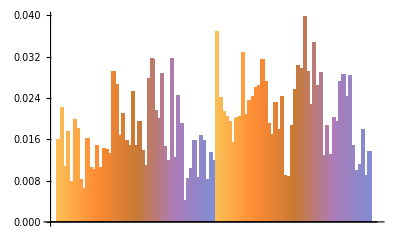

```mathematica
BarChart[{Join[MeansFromCenter["truth"], MeansFromCenter["truth2"],MeansFromCenter["truth3"], MeansFromCenter["mixed", "Truth", "TRUE"]], Join[MeansFromCenter["lies"], MeansFromCenter["lies2"],MeansFromCenter["lies3"], MeansFromCenter["mixed", "Truth", "FALSE"]]}]
```

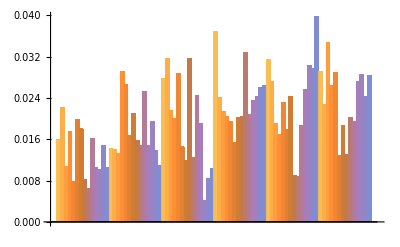

```mathematica
BarChart[{IndividualMeansFromCenter["truth"], IndividualMeansFromCenter["truth2"], IndividualMeansFromCenter["truth3"], IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]}]
```

```mathematica
IndividualMeansFromCenter["truth3"]
```

truth3

```mathematica
Mean[Join[IndividualMeansFromCenter["lies"], IndividualMeansFromCenter["lies2"], IndividualMeansFromCenter["lies3"]]]
```

0.0235469

```mathematica
Mean[IndividualMeansFromCenter["mixed"]]
```

0.0127355

```mathematica
Pupils[name_] :=
Block[{columns, dataset, allValues, center, grouped, groupedColumns, groupedValues, allMeans},
columns = {"Left Pupil Diameter", "Right Pupil Diameter"};
dataset=Select[ImportCsv[name], (#["Color"] == "Red")&];

grouped=dataset[GroupBy["Index"]];
groupedColumns = Table[grouped[[x]][All, columns], {x, 1, Length[grouped], 1}];
groupedValues = (Normal[Values[#]])& /@ groupedColumns;
allMeans = (Mean[Mean[{#[[1]], #[[2]]}]])& /@ groupedValues;
allMeans
]
```

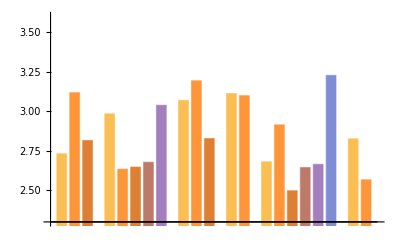

```mathematica
BarChart[{Pupils["truth"], Pupils["truth2"], Pupils["truth3"], Pupils["lies"], Pupils["lies2"], Pupils["lies3"]}, PlotRange->{{2.3,3.6}}]
```

```mathematica
Mean[Join[Pupils["truth"], Pupils["truth2"], Pupils["truth3"]]]
```

2.88514

```mathematica
Mean[Join[Pupils["lies"], Pupils["lies2"], Pupils["lies3"]]]
```

```mathematica
2.8233147
```

```mathematica
colors = (If[# == "FALSE",Red,Blue])& /@Normal[Values[((#[[1]])&/@ImportCsv["mixed"][GroupBy["Index"]])[All, "Truth"]]]
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

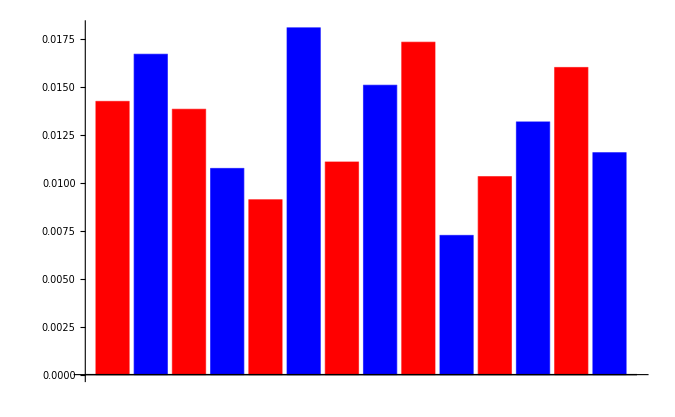

```mathematica
BarChart[IndividualMeansFromCenter["mixed"], ChartStyle-> colors]
```

```mathematica
TimeToAnswer[name_] := 
Block[{dataset, grouped, times},
dataset = ImportCsv[name];
grouped = dataset[GroupBy["Index"]];
times = Table[grouped[[x]][All, "Total Time"], {x, 1, Length[grouped], 1}];
(Last[#] - First[#])& /@ times
]
```

```mathematica
baselineTime = Mean[TimeToAnswer["truth3"]]
```

1.38023

```mathematica
baselineEye = Mean[IndividualMeansFromCenter["truth3"]]
```

0.0190438

```mathematica
EyeDiffFromBaseline[names_, baseline_]:=
Flatten[(Block[{means},
means = MeansFromCenter[#];
(Abs[baseline - #])& /@ means
])& /@ names]
```

```mathematica
EyeDiffFromBaseline[{"truth","truth2", "truth3"}, baselineEye]
```

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

Drop::drop: Cannot drop positions 1 through 1 in {}.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

Drop::drop: Cannot drop positions 1 through 1 in {}.

General::stop: Further output of Drop::drop will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[{},0.980956].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

{Mean[Drop[{},0.980956]],Mean[Drop[{},0.980956]],Mean[Drop[{},0.980956]]}